# LodewykJansenvanRensburg/ApproximateSpectra

The goal is to understand the spectrum of unitary pencils in free Haar unitary variables and this code allows one the experimentally test results using large unitary Haar distributed random matrices

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ReferencePages"

"Symbols"

"AnalyzeCharPoly.nb"DocumentationEnglishSymbolsAnalyzeCharPoly.nb

"AnalyzeTupleSpectrum.nb"DocumentationEnglishSymbolsAnalyzeTupleSpectrum.nb

"EstimateSpectralRadius.nb"DocumentationEnglishSymbolsEstimateSpectralRadius.nb

"FindTracePreservingTuple.nb"DocumentationEnglishSymbolsFindTracePreservingTuple.nb

"GeneratesFullMatrixAlgebraQ.nb"DocumentationEnglishSymbolsGeneratesFullMatrixAlgebraQ.nb

"MomentMatrix.nb"DocumentationEnglishSymbolsMomentMatrix.nb

"PlotEigenvaluesWithSpectralRadius.nb"DocumentationEnglishSymbolsPlotEigenvaluesWithSpectralRadius.nb

"PrintTuple.nb"DocumentationEnglishSymbolsPrintTuple.nb

"RandomSelfAdjointMatrixTuple.nb"DocumentationEnglishSymbolsRandomSelfAdjointMatrixTuple.nb

"SpectralRadiusFitPlot.nb"DocumentationEnglishSymbolsSpectralRadiusFitPlot.nb

"SpectralRadiusHistogramPlotWithFitGUE.nb"DocumentationEnglishSymbolsSpectralRadiusHistogramPlotWithFitGUE.nb

"SpectralRadiusHistogramPlotWithFit.nb"DocumentationEnglishSymbolsSpectralRadiusHistogramPlotWithFit.nb

"SpectralRadiusVarianceFitPlot.nb"DocumentationEnglishSymbolsSpectralRadiusVarianceFitPlot.nb

"Tutorials"

"Kernel"

"ApproximateSpectra.wl"KernelApproximateSpectra.wl

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

```mathematica
img=Import["/home/lodewyk/Desktop/paclet_Screen_saver.jpeg"]
```

-Graphics-

### Basic Description

This package provides tools for exploring the spectra of random matrices through the lens of free probability. The central idea is that as the size of certain random matrices grows, their spectral behavior converges to that of a deterministic operator predicted by free probability theory. The code focuses on degree-1 matrix polynomials (linear combinations of large random matrices and unitaries) and generates plots of their spectra. These visualizations serve as a bridge between finite-dimensional random matrix models and the limiting spectral distribution, helping us develop intuition and insight into the structure of the limiting operator.

### Details

Visualize Spectra

### Primary Context

LodewykJansenvanRensburg`ApproximateSpectra`

### Main Guide Page

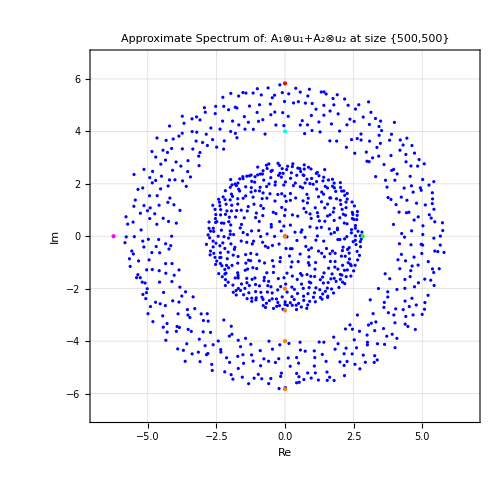
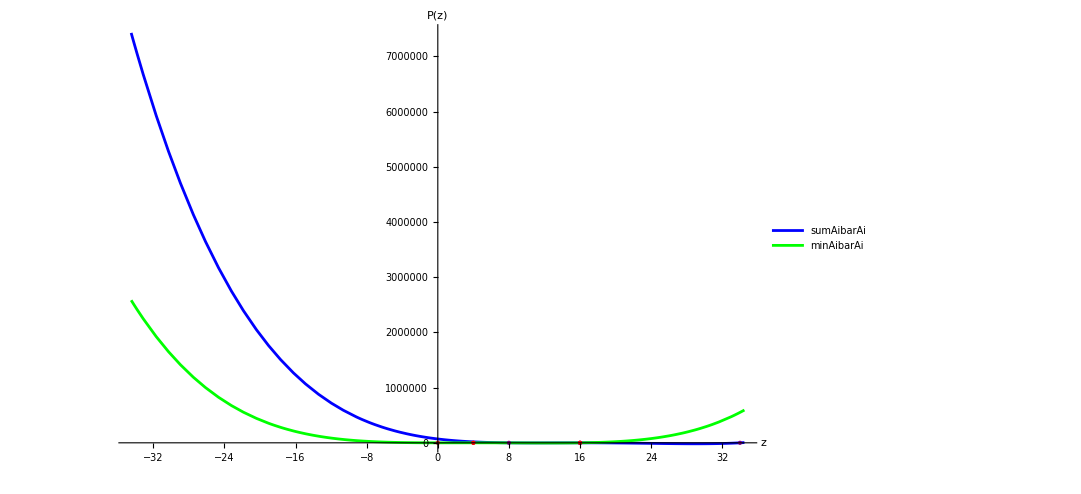
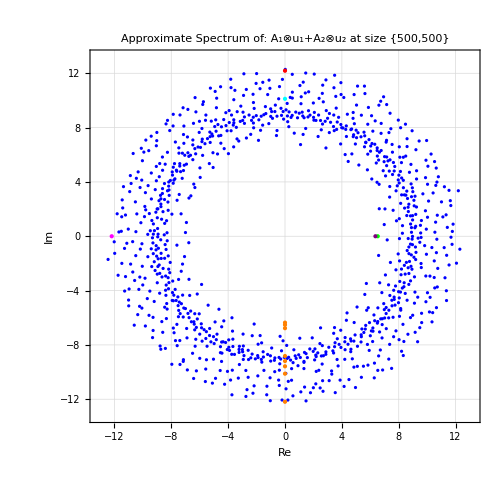
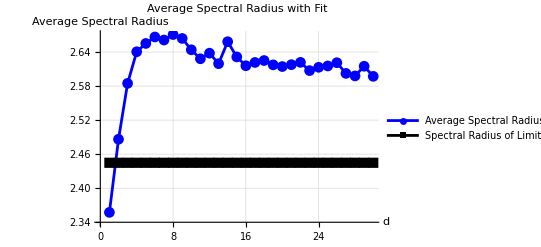
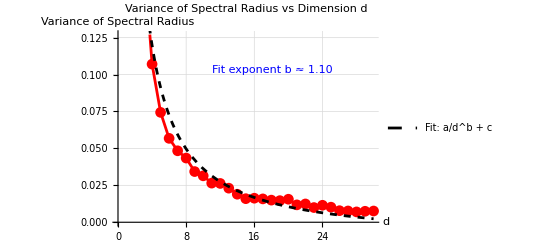
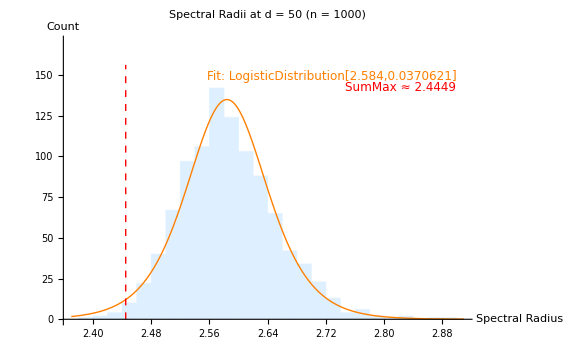
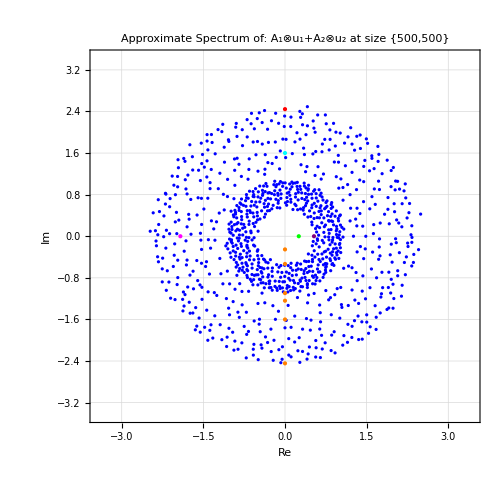
## Examples Initialization for Examples PacletDirectoryLoad["~/Documents/Wolfram/MyPaclets/LodewykJansenvanRensburg__ApproximateSpectra"]; Needs["LodewykJansenvanRensburg`ApproxSpectra`"]; Basic Examples Generate Random Haar Distributed dxd Unitaries (* Run to generate new unitaries*) d = 500; (*750 nice size to work with*) Un1 = RandomVariate[CircularUnitaryMatrixDistribution[d]]; Un2 = RandomVariate[CircularUnitaryMatrixDistribution[d]]; U = {Un1,Un2}; Create Coefficient Tuples A1 and A2 (* Choice of Matrix Tuple *) A = { {{5, 6}, {0, 2} }, {{3, 0}, {0, 2}} }; (* Visualize Coefficient Tuple *) PrintTuple[A]; "A"1" = "(5 | 6 0 | 2) "A"2" = "(3 | 0 0 | 2) Analyze the Spectrum of the Unitary Pencil with Matrix Coefficients (* Analyzing Spectra *) AnalyzeTupleSpectrum[A,U,PlotStyle -> "2D"] "===================================================================================================" " AnalyzeTupleSpectrum: " "=================================================================================================== " "Sqrt of eig values of A1bar ⊗ A1 + A2bar ⊗ A2: "{5.83095,4.,4.,2.82843} "Sqrt of eig values of A1bar ⊗ A1 - A2bar ⊗ A2 : "{4.,2.,2.,0.}" " "Sqrt of eig values of A1bar ⊗ A1 + A2bar ⊗ A2, and A1bar ⊗ A1 - A2bar ⊗ A2: "{0.,2.,2.82843,4.,5.83095} "===================================================================================================" "" -Graphics- | "Legend" 5.83095 ": OuterSpec (spectral rad). " 4. ": Inner Rad (larger)." 2.82843 ": Outer Rad (smaller)." 0. 6.245 ": Norm2Vneum." {0.,2.,2.82843,4.,5.83095} Deep dive into determining the radii of the Anulli AnalyzeCharPoly[A, True]; "============================================================================================" "Analyzing Characteristic Polynomial of A1bar ⊗ A1 + A2bar ⊗ A2 and A1bar ⊗ A1 - A2bar ⊗ A2 : " "========================================================================================== " -Graphics-"Root" | "Multp" | "Sqrt(Abs of Root)" 8. | 1. | 2.82843 16. | 2 | 4. 34. | 1. | 5.83095 "Root" | "Multp" | "Sqrt(Abs of Root)" 0. | 1. | 0. 4. | 2 | 2. 16. | 1. | 4. "========= Additional Info ============= " "Characteristic Polynomial of A1bar ⊗ A1 + A2bar ⊗ A2: "69632-19456 z+1872 z^2-74 z^3+z^4 "Matrix: A1bar ⊗ A1 + A2bar ⊗ A2 = "(34 | 30 | 30 | 36 0 | 16 | 0 | 12 0 | 0 | 16 | 12 0 | 0 | 0 | 8) " Characteristic Polynomial of A1bar ⊗ A1 - A2bar ⊗ A2: "-256 z+144 z^2-24 z^3+z^4 "Matrix: A1bar ⊗ A1 - A2bar ⊗ A2 = "(16 | 30 | 30 | 36 0 | 4 | 0 | 12 0 | 0 | 4 | 12 0 | 0 | 0 | 0) "========= End ============= " Another Example where we randomly select the coefficient tuple {A1, A2} numTries = 15; (* Solving Solutions based on random numebers. Sometimes no solution, but then just try again with different random numbers *) intRange = 10; (* Some integer entries of coefficient matrices are taken randomly between this range*) A = FindTracePreservingTuple[numTries, {-intRange, intRange}, False]; PrintTuple[A]; (* Analyzing Spectra *) AnalyzeTupleSpectrum[A,U,PlotStyle -> "2D"] "A"1" = "(-10 | -3.40986 3 | 7.20243) "A"2" = "(-3 | 2 5.52287 | -9) "===================================================================================================" " AnalyzeTupleSpectrum: " "=================================================================================================== " "Sqrt of eig values of A1bar ⊗ A1 + A2bar ⊗ A2: "{12.1861,9.57681,6.77056,6.52307} "Sqrt of eig values of A1bar ⊗ A1 - A2bar ⊗ A2 : "{10.1195,9.18787,8.81754,6.3591}" " "Sqrt of eig values of A1bar ⊗ A1 + A2bar ⊗ A2, and A1bar ⊗ A1 - A2bar ⊗ A2: "{6.3591,6.52307,6.77056,8.81754,9.18787,9.57681,10.1195,12.1861} "===================================================================================================" "" -Graphics- | "Legend" 12.1861 ": OuterSpec (spectral rad). " 10.1195 ": Inner Rad (larger)." 6.52307 ": Outer Rad (smaller)." 6.3591 ": Inner Rad (smaller)." 12.1861 ": Norm2Vneum." {6.3591,6.52307,6.77056,8.81754,9.18787,9.57681,10.1195,12.1861} Other Spectral Statistics that " converge to the limiting spectrum ". (* Parameters *) k = 2; (* Size of Coefficient Matrix*) g = 2; (* Length of tuple, must be 2 for AnalyzeTupleSpectrum*) SampleSize = 200; (* Average over this amount of matrices *) MatrixStopSize = 30; (* Max size of matrices *) MatrixStarSize = 1; (* Min size of matrices *) (* Randomly Generate Coefficient Matrix*) A = (1/2)*RandomSelfAdjointMatrixTuple[k, g]; A = RandomComplex[{},{g,k,k}]; PrintTuple[A] (* Plots the Averaged Spectral Radius as size d grows *) SpectralRadiusFitPlot[A, SampleSize, MatrixStarSize, MatrixStopSize] (* Plots the Variance in Our Data for large d *) SpectralRadiusVarianceFitPlot[A, SampleSize, MatrixStarSize, MatrixStopSize] (* Plots an approximation of the distribution of the spectral radius at a fixed size*) (* What does this do? Given a fixed matrix size d, is computes numRealization times the spec_rad of our realiztion, and plots the historgram of bins. That is the area under the histrogram represents the probability that spec_rad will fall inside a given interval. *) d = 50; numRealization = 1000; SpectralRadiusHistogramPlotWithFit[A, numRealization, 50] (* Plots the spectrum of one realization *) AnalyzeTupleSpectrum[A,U,PlotStyle -> "2D"] "A"1" = "(0.896616+0.471306 ⅈ | 0.043753+0.746957 ⅈ 0.0861909+0.455626 ⅈ | 0.892889+0.611507 ⅈ) "A"2" = "(0.450868+0.593407 ⅈ | 0.882552+0.682738 ⅈ 0.994552+0.850207 ⅈ | 0.100772+0.947376 ⅈ) -Graphics- -Graphics- -Graphics- "===================================================================================================" " AnalyzeTupleSpectrum: " "=================================================================================================== " "Sqrt of eig values of A1bar ⊗ A1 + A2bar ⊗ A2: "{2.44488,1.09407,0.253289,0.253289} "Sqrt of eig values of A1bar ⊗ A1 - A2bar ⊗ A2 : "{1.60073,1.60073,1.23965,0.532484}" " "Sqrt of eig values of A1bar ⊗ A1 + A2bar ⊗ A2, and A1bar ⊗ A1 - A2bar ⊗ A2: "{0.253289,0.532484,1.09407,1.23965,1.60073,2.44488} "===================================================================================================" "" -Graphics- | "Legend" 2.44488 ": OuterSpec (spectral rad). " 1.60073 ": Inner Rad (larger)." 0.253289 ": Outer Rad (smaller)." 0.532484 ": Inner Rad (smaller)." 1.92253 ": Norm2Vneum." {0.253289,0.532484,1.09407,1.23965,1.60073,2.44488}

## Source & Additional Information

### Creator

Author Name

### Source Control Repository

https://github.com/UserName/MyPaclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

14.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.